# Report

Contributor: 
Azzuhra Syifa - 24202201
Siti Nurihabajuri Binti Arsyi  - 24305304

## Predictor-Corrector (ABM4) method

In this report, four-step explicit Adams-Bashforth method is used as the predictor. The starting values are computed using Runge- Kutta method of order four. The approximation is then improved using the three-step implicit Adams-Moulton method as the corrector. This method is denoted as ABM4 in this report.

### The Computation of Logistic Equation Population using ABM4 and variety of K values

```mathematica
(*Actual population data*)realData={{2015,1698100},{2016,1717700},{2017,1744100},{2018,1762800},{2019,1768800},{2020,1740400},{2021,1740000},{2022,1740900},{2023,1772600},{2024,1800500},{2025,1803300}};

(*Population model*)
PopulationModel[K_]:=Module[{r=0.0114762,h=1,t0=0,tEnd=10,P0=1698100,f,t,P,k1,k2,k3,k4,Ppred,Pnext,n},
f[t_,P_]:=r(1-P/K) P; (*Logistic equation*)
t=Range[t0,tEnd,h];
P={P0};
(*RK4 starting value*)
Do[k1=h f[t[[i]],P[[i]]];
k2=h f[t[[i]]+h/2,P[[i]]+k1/2];
k3=h f[t[[i]]+h/2,P[[i]]+k2/2];
k4=h f[t[[i]]+h,P[[i]]+k3];
AppendTo[P,P[[i]]+(k1+2 k2+2 k3+k4)/6],{i,1,3}];
(*AB4 predictor+AM4 corrector*)
Do[Ppred=P[[n]]+h/24 (55 f[t[[n]],P[[n]]]-59 f[t[[n-1]],P[[n-1]]]+37 f[t[[n-2]],P[[n-2]]]-9 f[t[[n-3]],P[[n-3]]]);
Pnext=P[[n]]+h/24 (9 f[t[[n+1]],Ppred]+19 f[t[[n]],P[[n]]]-5 f[t[[n-1]],P[[n-1]]]+f[t[[n-2]],P[[n-2]]]);
AppendTo[P,Pnext],{n,4,Length[t]-1}];
Transpose[{Range[2015,2025],P}]]

(*Comparison plot: Adjustable carrying capacity, K*)
Manipulate[ListLinePlot[{realData,PopulationModel[K]},PlotLegends->{"Actual Data","ABM4 Population Data"},AxesLabel->{"Year","Population"},PlotLabel->Row[{"Population Comparison (K = ",NumberForm[K,DigitBlock->3],")"}],PlotRange->All,ImageSize->Large],{K,1500000,5000000,50000}]
```

### The Comparison of Actual Population vs Logistic Equation Population

#### Graph

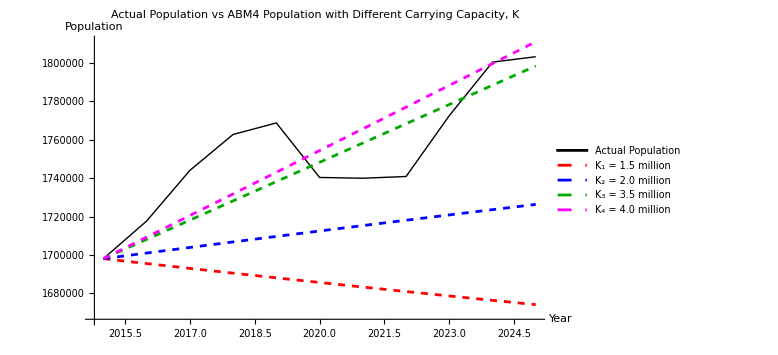

```mathematica
Subscript[modelK, 1]=PopulationModel[1500000];
Subscript[modelK, 2]=PopulationModel[2000000];
Subscript[modelK, 3]=PopulationModel[3500000];
Subscript[modelK, 4]=PopulationModel[4000000];
ListLinePlot[{realData,Subscript[modelK, 1],Subscript[modelK, 2],Subscript[modelK, 3],Subscript[modelK, 4]},PlotStyle->{{Black,Thick},{Red,Dashed},{Blue,Dashed},{Darker[Green],Dashed},{Magenta,Dashed}},PlotLegends->{"Actual Population","K_1 = 1.5 million","K_2 = 2.0 million","K_3 = 3.5 million","K_4 = 4.0 million"},AxesLabel->{"Year","Population"},PlotLabel->"Actual Population vs ABM4 Population with Different Carrying Capacity, K",PlotRange->All,ImageSize->Large]
```

#### Table

```mathematica
ErrorTable[K_]:=Module[{model,years,actual},model=PopulationModel[K][[All,2]];
years=realData[[All,1]];
actual=realData[[All,2]];
Table[{years[[i]],actual[[i]],Round[model[[i]]],Abs[Round[model[[i]]-actual[[i]]]],NumberForm[Abs[100 (model[[i]]-actual[[i]])/actual[[i]]],{4,2}]},{i,Length[years]}]];
Manipulate[Column[{Style[Row[{"Current value of K = ",NumberForm[K,DigitBlock->3]}],Bold],TableForm[ErrorTable[K],TableHeadings->{None,{"Year","Actual Population","AB4–AM4 Population","Absolute Error","Relative Error (%)"}}]}],{K,1500000,5000000,50000}]
```

```mathematica
TableForm[ErrorTable[1500000],TableHeadings->{None,{"Year","Actual Population","ABM4 Population","Absolute Error","Relative Error(%)"}}]
```

Year | Actual Population | ABM4 Population | Absolute Error | Relative Error(%)
2015 | 1698100 | 1698100 | 0 | 0
2016 | 1717700 | 1695545 | 22155 | 1.29
2017 | 1744100 | 1693026 | 51074 | 2.93
2018 | 1762800 | 1690544 | 72256 | 4.10
2019 | 1768800 | 1688097 | 80703 | 4.56
2020 | 1740400 | 1685685 | 54715 | 3.14
2021 | 1740000 | 1683308 | 56692 | 3.26
2022 | 1740900 | 1680964 | 59936 | 3.44
2023 | 1772600 | 1678653 | 93947 | 5.30
2024 | 1800500 | 1676375 | 124125 | 6.89
2025 | 1803300 | 1674128 | 129172 | 7.16

```mathematica
TableForm[ErrorTable[2000000],TableHeadings->{None,{"Year","Actual Population","ABM4 Population","Absolute Error","Relative Error(%)"}}]
```

Year | Actual Population | ABM4 Population | Absolute Error | Relative Error(%)
2015 | 1698100 | 1698100 | 0 | 0
2016 | 1717700 | 1701030 | 16670 | 0.97
2017 | 1744100 | 1703936 | 40164 | 2.30
2018 | 1762800 | 1706819 | 55981 | 3.18
2019 | 1768800 | 1709679 | 59121 | 3.34
2020 | 1740400 | 1712516 | 27884 | 1.60
2021 | 1740000 | 1715329 | 24671 | 1.42
2022 | 1740900 | 1718120 | 22780 | 1.31
2023 | 1772600 | 1720887 | 51713 | 2.92
2024 | 1800500 | 1723632 | 76868 | 4.27
2025 | 1803300 | 1726354 | 76946 | 4.27

```mathematica
TableForm[ErrorTable[3500000],TableHeadings->{None,{"Year","Actual Population","ABM4 Population","Absolute Error","Relative Error(%)"}}]
```

Year | Actual Population | ABM4 Population | Absolute Error | Relative Error(%)
2015 | 1698100 | 1698100 | 0 | 0
2016 | 1717700 | 1708134 | 9566 | 0.56
2017 | 1744100 | 1718172 | 25928 | 1.49
2018 | 1762800 | 1728211 | 34589 | 1.96
2019 | 1768800 | 1738252 | 30548 | 1.73
2020 | 1740400 | 1748293 | 7893 | 0.45
2021 | 1740000 | 1758335 | 18335 | 1.05
2022 | 1740900 | 1768376 | 27476 | 1.58
2023 | 1772600 | 1778416 | 5816 | 0.33
2024 | 1800500 | 1788454 | 12046 | 0.67
2025 | 1803300 | 1798489 | 4811 | 0.27

```mathematica
TableForm[ErrorTable[4000000],TableHeadings->{None,{"Year","Actual Population","ABM4 Population","Absolute Error","Relative Error(%)"}}]
```

Year | Actual Population | ABM4 Population | Absolute Error | Relative Error(%)
2015 | 1698100 | 1698100 | 0 | 0
2016 | 1717700 | 1709324 | 8376 | 0.49
2017 | 1744100 | 1720567 | 23533 | 1.35
2018 | 1762800 | 1731828 | 30972 | 1.76
2019 | 1768800 | 1743107 | 25693 | 1.45
2020 | 1740400 | 1754402 | 14002 | 0.80
2021 | 1740000 | 1765713 | 25713 | 1.48
2022 | 1740900 | 1777039 | 36139 | 2.08
2023 | 1772600 | 1788380 | 15780 | 0.89
2024 | 1800500 | 1799734 | 766 | 0.04
2025 | 1803300 | 1811102 | 7802 | 0.43

## Comparison between ABM4 and Milne-Simpson

Comparison Table: Actual Data vs. ABM4 vs. Milne-Sims (K = 3.5M)

Year | Actual | ABM4 | Error ABM4 (%) | Milne-Sims | Error Milne (%)
2015 | 1698100 | 1698100 | 0 | 1698100 | 0
2016 | 1717700 | 1708134 | 0.56 | 1708134 | 0.56
2017 | 1744100 | 1718172 | 1.49 | 1718172 | 1.49
2018 | 1762800 | 1728211 | 1.96 | 1728211 | 1.96
2019 | 1768800 | 1738252 | 1.73 | 1738252 | 1.73
2020 | 1740400 | 1748293 | 0.45 | 1748293 | 0.45
2021 | 1740000 | 1758335 | 1.05 | 1758335 | 1.05
2022 | 1740900 | 1768376 | 1.58 | 1768376 | 1.58
2023 | 1772600 | 1778416 | 0.33 | 1778416 | 0.33
2024 | 1800500 | 1788454 | 0.67 | 1788454 | 0.67
2025 | 1803300 | 1798489 | 0.27 | 1798489 | 0.27

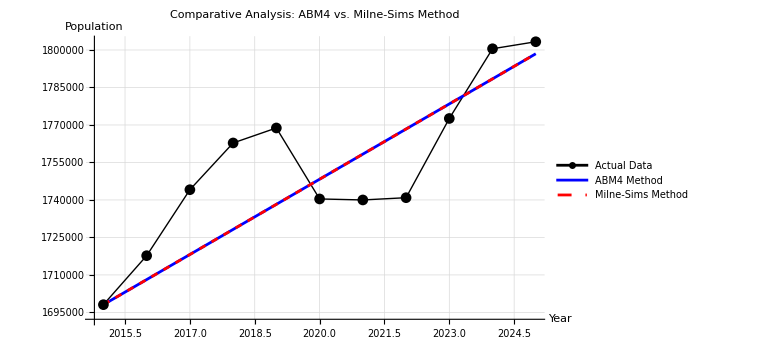

```mathematica
r=0.0114762;
K=3500000;
h=1;
t0=0;
tEnd=10;
P0=1698100;

f[t_,P_]:=r (1-P/K) P

tValues=Range[t0,tEnd,h];
yearValues=Range[2015,2025];

GetRK4Points[initialP_]:=Module[{pList={initialP},k1,k2,k3,k4},Do[k1=h f[tValues[[i]],pList[[i]]];
k2=h f[tValues[[i]]+h/2,pList[[i]]+k1/2];
k3=h f[tValues[[i]]+h/2,pList[[i]]+k2/2];
k4=h f[tValues[[i]]+h,pList[[i]]+k3];
AppendTo[pList,pList[[i]]+(k1+2 k2+2 k3+k4)/6],{i,1,3}];
pList]

pABM=GetRK4Points[P0];
Do[pPred=pABM[[n]]+h/24 (55 f[tValues[[n]],pABM[[n]]]-59 f[tValues[[n-1]],pABM[[n-1]]]+37 f[tValues[[n-2]],pABM[[n-2]]]-9 f[tValues[[n-3]],pABM[[n-3]]]);
pNext=pABM[[n]]+h/24 (9 f[tValues[[n+1]],pPred]+19 f[tValues[[n]],pABM[[n]]]-5 f[tValues[[n-1]],pABM[[n-1]]]+f[tValues[[n-2]],pABM[[n-2]]]);
AppendTo[pABM,pNext],{n,4,Length[tValues]-1}];

pMilne=GetRK4Points[P0];
Do[pPred=pMilne[[n-3]]+(4 h/3) (2 f[tValues[[n]],pMilne[[n]]]-f[tValues[[n-1]],pMilne[[n-1]]]+2 f[tValues[[n-2]],pMilne[[n-2]]]);
pNext=pMilne[[n-1]]+(h/3) (f[tValues[[n+1]],pPred]+4 f[tValues[[n]],pMilne[[n]]]+f[tValues[[n-1]],pMilne[[n-1]]]);
AppendTo[pMilne,pNext],{n,4,Length[tValues]-1}];

realData={1698100,1717700,1744100,1762800,1768800,1740400,1740000,1740900,1772600,1800500,1803300};

comparisonTable=Table[{yearValues[[i]],realData[[i]],Round[pABM[[i]]],NumberForm[Abs[100 (pABM[[i]]-realData[[i]])/realData[[i]]],{4,2}],Round[pMilne[[i]]],NumberForm[Abs[100 (pMilne[[i]]-realData[[i]])/realData[[i]]],{4,2}]},{i,1,Length[yearValues]}];

Print[Style["Comparison Table: Actual Data vs. ABM4 vs. Milne-Sims (K = 3.5M)",Bold,14]];
TableForm[comparisonTable,TableHeadings->{None,{"Year","Actual","ABM4","Error ABM4 (%)","Milne-Sims","Error Milne (%)"}}]

ListLinePlot[{Transpose[{yearValues,realData}],Transpose[{yearValues,pABM}],Transpose[{yearValues,pMilne}]},PlotStyle->{Directive[Black,Thick],Blue,Directive[Red,Dashed]},PlotLegends->{"Actual Data","ABM4 Method","Milne-Sims Method"},PlotMarkers->{Automatic,None,None},AxesLabel->{"Year","Population"},PlotLabel->"Comparative Analysis: ABM4 vs. Milne-Sims Method",GridLines->Automatic,ImageSize->Large]
```

## Predicted Population (2026 - 2030) using ABM4

Adams-Bashforth-Moulton Prediction (K = 3,500,000)

Year | Predicted Population
2025 | 1798489
2026 | 1808521
2027 | 1818550
2028 | 1828574
2029 | 1838592
2030 | 1848605

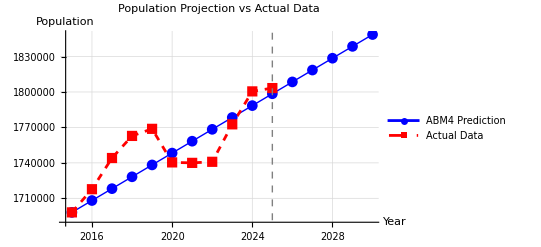

```mathematica
r=0.0114762;
K=3500000; 
h=1;
t0=0;
tForecastEnd=15; 
P0=1698100;

f[t_,P_]:=r (1-P/K) P

t=Range[t0,tForecastEnd,h];
yearForecast=Range[2015,2015+tForecastEnd];

P={P0};
Do[k1=h f[t[[i]],P[[i]]];
k2=h f[t[[i]]+h/2,P[[i]]+k1/2];
k3=h f[t[[i]]+h/2,P[[i]]+k2/2];
k4=h f[t[[i]]+h,P[[i]]+k3];
AppendTo[P,P[[i]]+(k1+2 k2+2 k3+k4)/6],{i,1,3}];

Do[Ppred=P[[n]]+h/24 (55 f[t[[n]],P[[n]]]-59 f[t[[n-1]],P[[n-1]]]+37 f[t[[n-2]],P[[n-2]]]-9 f[t[[n-3]],P[[n-3]]]);
Pnext=P[[n]]+h/24 (9 f[t[[n+1]],Ppred]+19 f[t[[n]],P[[n]]]-5 f[t[[n-1]],P[[n-1]]]+f[t[[n-2]],P[[n-2]]]);
AppendTo[P,Pnext],{n,4,Length[t]-1}];

realData={{2015,1698100},{2016,1717700},{2017,1744100},{2018,1762800},{2019,1768800},{2020,1740400},{2021,1740000},{2022,1740900},{2023,1772600},{2024,1800500},{2025,1803300}};

forecastResults=Table[{yearForecast[[i]],Round[P[[i]]]},{i,11,Length[yearForecast]}];
Print[Style["Adams-Bashforth-Moulton Prediction (K = 3,500,000)",Bold,16]];
TableForm[forecastResults,TableHeadings->{None,{"Year","Predicted Population"}}]

ListLinePlot[{Transpose[{yearForecast,P}],realData},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Red,Dashed}},GridLines->Automatic,AxesLabel->{"Year","Population"},PlotLabel->"Population Projection vs Actual Data",PlotLegends->{"ABM4 Prediction","Actual Data"},Epilog->{Dashed,Gray,Line[{{2025,0},{2025,2000000}}]}]
```